### Schrödinger Equation Solver Tool:

This code simulates and visualizes the time evolution of a quantum wave function (starting as a Gaussian wave packet) as it moves through different potential landscapes.
The process works like this:

Initial State: We start with a Gaussian wave packet (the gaussianPacket function), which represents a quantum particle with a reasonably well-defined position and momentum. In the example, it starts at position -5 with a positive momentum (moving to the right).
Time Evolution: The Schrödinger equation solver then calculates how this wave packet evolves over time according to the time-dependent Schrödinger equation:
i·ħ·∂ψ/∂t = -ħ.b2/(2m)·∂.b2ψ/∂x.b2 + V(x)·ψ
Potential Influence: The potential function (potentialFunc) affects how the wave packet moves and changes. Different potentials produce different behaviors:

Free particle: The wave packet simply spreads out while moving
Barrier: The wave packet partially reflects and partially tunnels through
Harmonic oscillator: The wave packet oscillates back and forth
Double well: The wave packet can tunnel between the two wells


Visualization: The animation shows the probability density (|ψ|.b2) over time, which tells you the probability of finding the particle at different positions as time passes.

This is a powerful tool for teaching quantum mechanics because it lets students see quantum phenomena like:

Wave packet spreading
Quantum tunneling
Quantum reflection
Quantum superposition
Wave-like behavior of particles

```mathematica
Quit
```

```mathematica
(*Set up natural units*)
ħ=1;
m=1;

(*Define a function to solve and visualize the time-dependent Schrödinger equation*)
solveSchrodinger[potentialFunc_,initialState_,tMax_]:=Module[{psi,x,t,xMin=-10,xMax=10,sol,normConst,potentialPlot,maxPotential},
(*Ensure the domain is appropriate*)
xMin=-10;
xMax=10;
(*Find maximum potential value for scaling*)
maxPotential=Max[Table[potentialFunc[x],{x,xMin,xMax,0.1}]];
If[maxPotential==0,maxPotential=1];(*Avoid division by zero*)(*Create a plot of the potential for reference*)potentialPlot=Plot[potentialFunc[x],{x,xMin,xMax},PlotStyle->{Thick,Red},PlotRange->All,PlotLabel->"Potential Energy Function"];
(*Show the potential first*)
Print["Potential Energy Function:"];
Print[potentialPlot];
(*Solve the time-dependent Schrödinger equation*)
Print["Solving the Schrödinger equation..."];
sol=NDSolve[{(*Time-dependent Schrödinger equation with ħ=1,m=1*)I*D[psi[x,t],t]==-0.5*D[psi[x,t],{x,2}]+potentialFunc[x]*psi[x,t],(*Initial condition*)psi[x,0]==initialState[x],(*Boundary conditions (wave function vanishes at boundaries)*)
psi[xMin,t]==0,psi[xMax,t]==0},psi,{x,xMin,xMax},{t,0,tMax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100}}];
(*Create an animation of the probability density*)
Print["Time evolution of the probability density:"];
Animate[Module[{currentDensity,maxDensity,scaledPotential},
(*Get the current probability density*)
currentDensity=Abs[psi[x,tCurrent]/. sol]^2;
(*Scale the potential for visualization*)
scaledPotential=potentialFunc[x]/maxPotential*0.8;
(*Create the plot*)
Plot[{scaledPotential,currentDensity},{x,xMin,xMax},PlotRange->{0,1},PlotStyle->{{Thick,Dashed,Gray},{Thick,Blue}},Filling->{2->0},FillingStyle->Opacity[0.2,Blue],AxesLabel->{"Position","Probability Density"},PlotLegends->{"Scaled Potential","Probability Density"},PlotLabel->"Time = "<>ToString[NumberForm[tCurrent,{4,2}]],GridLines->Automatic,ImageSize->600]],{tCurrent,0,tMax,tMax/50},AnimationRate->1,DisplayAllSteps->False,AnimationRunning->False]]

(*Example usage:Free particle Gaussian wave packet*)
(*Define initial Gaussian wave packet*)
gaussianPacket[x_]:=Exp[-(x+5)^2/2]*Exp[I*2*x]

(*Define a few example potentials*)
freeParticle[x_]:=0
barrier[x_]:=If[Abs[x]<1,5,0]
harmonicOscillator[x_]:=0.1*x^2
doublePotentialWell[x_]:=0.5*(x^2-4)^2

(*Usage examples*)
(*Uncomment one of these lines to run:*)
```

Potential Energy Function:

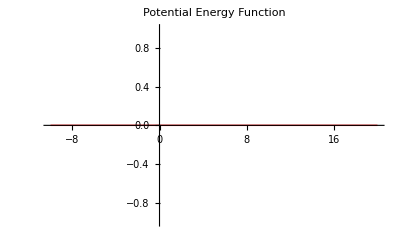

Solving the Schrödinger equation...

Time evolution of the probability density:

```mathematica
(*Example 1:Free particle*)
solveSchrodinger[freeParticle,gaussianPacket,5]
```

```mathematica
(*The narrower your initial position distribution (smaller Δx),the wider your momentum distribution must be (larger Δp) to satisfy the uncertainty principle.A wider momentum distribution means more extreme differences in velocity components,which leads to faster spreading of the wave packet.The uncertainty principle isn't just a limitation on measurement-it's a fundamental property of wave-like entities that has real,observable consequences like wave packet spreading.This is why free particles always spread out in quantum mechanics,while in classical mechanics a free particle would maintain its shape forever.
The uncertainty principle itself (Δx·Δp≥ħ/2) doesn't explicitly involve time,but time plays a critical role in how the uncertainty principle manifests in wave packet evolution:Initial condition (t=0):We start with a localized wave packet with position uncertainty Δx
Due to the uncertainty principle,this gives us momentum uncertainty Δp
Time evolution:At t=0,different momentum components are all aligned in phase
As time passes,these components evolve at different rates
For a free particle,the phase evolution is e^(iEt/ħ)=e^(ip.b2t/2mħ)
This reveals a profound point:the uncertainty principle forces an initially well-localized state to become increasingly delocalized as time progresses.You can think of it as the "cost" of having violated the equilibrium balance between position and momentum uncertainty being paid back over time.*)
```

Potential Energy Function:

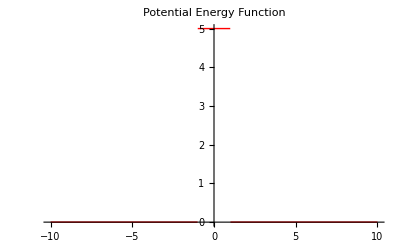

Solving the Schrödinger equation...

Time evolution of the probability density:

```mathematica
(*Example 2:Barrier scattering*)
solveSchrodinger[barrier,gaussianPacket,6]
```

Potential Energy Function:

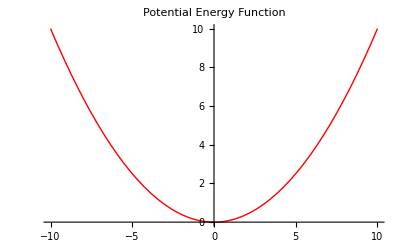

Solving the Schrödinger equation...

Time evolution of the probability density:

```mathematica
(*Example 3:Harmonic oscillator*)
solveSchrodinger[harmonicOscillator,gaussianPacket,12]
```

Potential Energy Function:

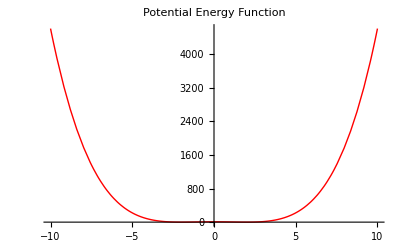

Solving the Schrödinger equation...

NDSolve::eerr: Warning: scaled local spatial error estimate of 14096.9 at t$145951 = 10. in the direction of independent variable x$145951 is much greater than the prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

Time evolution of the probability density:

```mathematica
(*Example 4:Double well potential*)
solveSchrodinger[doublePotentialWell,gaussianPacket,10]
```